```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];;
```

```mathematica
coords = {t,r ,θ,ϕ};
n=Length[coords];
M=1;μ=1;
solorder=2;
```

```mathematica
tt=Normal[Series[-(1-(2 M r)/(r^2+a^2 Cos[θ]^2)),{a,0,solorder}]];
rr=Normal[Series[(r^2+a^2 Cos[θ]^2)/(r^2-2 M r+a^2),{a,0,solorder}]];
θθ=Normal[Series[r^2+a^2 Cos[θ]^2,{a,0,solorder}]];
ϕϕ=Normal[Series[Sin[θ]^2(r^2+a^2+(2M a^2 r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)),{a,0,solorder}]];
tϕ=Normal[Series[-((2 a M r Sin[θ]^2)/(r^2+a^2 Cos[θ]^2)),{a,0,solorder}]];
metric={{tt,0,0,tϕ},{0,rr,0,0},{0,0,θθ,0},{tϕ,0,0,ϕϕ}};
inversemetric=Simplify[Inverse[metric]];
```

```mathematica
christoffel:=christoffel=Simplify[Table[(1/2)*Sum[(inversemetric[[i,s]])*
(D[metric[[s,j]],coords[[k]] ]+
D[metric[[s,k]],coords[[j]] ]-D[metric[[j,k]],coords[[s]] ]),{s,1,n}],
{i,1,n},{j,1,n},{k,1,n}] ];
listchristoffel:=Table[If[UnsameQ[christoffel[[i,j,k]],0],{ToString[Γ[i,j,k]],christoffel[[i,j,k]]}] ,{i,1,n},{j,1,n},{k,1,j}];
geodesic:=geodesic=Table[-Sum[christoffel[[i,j,k]]coords[[j]]' coords[[k]]',{j,1,n},
{k,1,n}],{i,1,n}];
listgeodesic:=Table[{"d/dτ"ToString[coords[[i]]'],"=",geodesic[[i]]},{i,1,n}];
```

```mathematica
a=3/10 M;
Li= Rationalize[3.422]M; (*u_tu_phi  (Covariant)*)
EEi= Rationalize[0.953];
ri= Rationalize[11.295];
```

```mathematica
uti=(EEi ϕϕ+Li tϕ)/(tϕ^2-tt ϕϕ)/.{θ-> π/2,r-> ri};
uϕi= -(EEi tϕ+Li tt)/(tϕ^2-tt ϕϕ)/.{θ-> π/2,r-> ri};
```

```mathematica
ivscond={uti,0,uθi,uϕi};(*Contravariant*)(*Velocities*)
uθi=Solve[(ivscond.metric.ivscond/.{r-> ri,θ->π/2})==-μ^2][[1]][[1]][[2]];
```

```mathematica
ics={0.0,ri,π/2,0.0}(*Coordinates*);
ivs=ivscond;(*Velocities*)
```

```mathematica
orbit[maxτi_,ivsi_,icsi_,iτ_]:=Block[{ivs,ics,i,soln},
ics=icsi;
ivs=ivsi;
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=NDSolve[deq,Join[coords,{coords[[2]]'}],{τ,iτ,iτ+maxτi},Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}},AccuracyGoal->16,PrecisionGoal->16,StartingStepSize->0.1,MaxSteps->∞];
soln]
us[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];uα=uα/.τ->τval;{uα}]
```

```mathematica
computeSoln[maxτi_,ivsi_,icsi_,iτ_]:=Block[{ivs,ics,i,soln},
ics=icsi;
ivs=ivsi;
deq=Table[coords[[i]]''[τ]==(geodesic[[i]]/.Join[Table[coords[[i]]'->coords[[i]]'[τ],{i,1,n}],Table[coords[[i]]->coords[[i]][τ],{i,1,n}]]),{i,1,n}];
deq=Join[deq,Table[coords[[i]]'[0]==ivs[[i]],{i,1,n}],Table[coords[[i]][0]==ics[[i]],{i,1,n}]];
soln=Reap[NDSolve[deq,{},{τ,iτ,iτ+maxτi},Method->{"EventLocator","Event"->Chop[Cos[coords[[3]][τ]]],"EventAction":>Sow[{coords[[2]][τ],coords[[2]]'[τ]}],Direction->1,"EventLocationMethod"->"LinearInterpolation",Method->{StiffnessSwitching,Method->{ExplicitRungeKutta,Automatic}}},AccuracyGoal->16,PrecisionGoal->16,StartingStepSize->0.1,MaxSteps->∞]];
soln]
us[solni_,τval_]:=Block[{xα,uα},xα=Table[coords[[i]][τ]/.solni,{i,1,n}]//Flatten; uα=D[xα,τ];uα=uα/.τ->τval;{uα}]
```

```mathematica
tMaxPlot=10000;
```

```mathematica
soln=orbit[tMaxPlot,ivs,ics,0];
```

```mathematica
ParametricPlot3D[{r[s] Sin[θ[s]] Cos[ϕ[s]],r[s] Sin[θ[s]] Sin[ϕ[s]],r[s] Cos[θ[s]]}/.soln,{s,0,tMaxPlot},PlotRange->All,PlotStyle->{Black,Thick},PlotPoints->100,ViewPoint->{15,15,15}]
```

-Graphics3D-

```mathematica
maxτ= 5000000M; 
PoincareSurface=computeSoln[maxτ,ivscond,ics,0][[-1,1]];
```

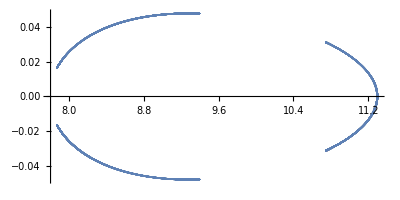

```mathematica
ListPlot[{PoincareSurface},AspectRatio->0.5,PlotRange->All]
```

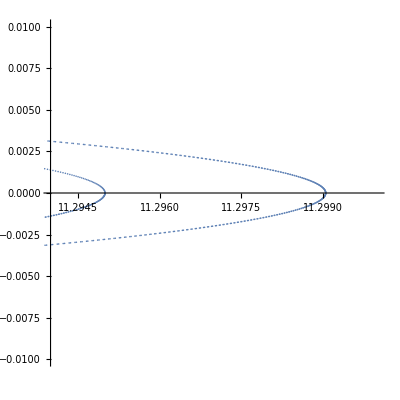

```mathematica
ListPlot[{PoincareSurface},AspectRatio->1,PlotRange->{{11.294,11.3},{-0.01,0.01}}]
```